Université Pierre et Marie Curie |                                                                          | UE 4M062 Mathematica

________________________________________________________________________

M 3 : Applications EDO avec Mathematica
________________________________________________________________________

## Exercices du Préambule

Le fichier doit être renommé exactement comme ceci :
	M1VotrenomPrenom.nb
Cela permet à vos enseignants de s’y retrouver et de ne pas avoir à renommer tous les fichiers. Merci.
	Votrenom avec une seule majuscule
	Prenom avec une seule majuscule
	Pas de blanc, ni souligné, ni accent, ni symbole particulier
Ce fichier doit être déposé sur MOODLE à la fin de la séance, et/ou avant la fin de la semaine de la séance.

## I. Objectif général et Présentation

## II. Calcul matriciel

Tous les calculs sont effectuées avec des matrices réelles carrées d’ordre 2 sans aucune perte de généralité, car toutes les opérations ci-dessous sont vérifiées pour n’importe quel ordre, et n’importe quelles matrices.

### → B. Opérations de base sur des matrices *

Pour saisir une matrice, le plus simple est d’utiliser la suite de menus :
							Insert ⊳ Create Table/Matrix/  ⊳ New

ou encore les raccourcis clavier indiqués dans ce dernier menu.

On peut aussi utiliser la palette : 			Palettes ⊳ Basic Math Assistant

#### → 1) Saisir les matrices suivantes :

matM=(a | b
c | d) et matN=(α | β
γ | δ)

```mathematica
matM= ({{a, b}, {c, d}})
```

{{a,b},{c,d}}

```mathematica
matN= ({{α, β}, {γ, δ}})
```

{{α,β},{γ,δ}}

#### → 2) Calculez la somme matricielle : matM+2matN

```mathematica
matM+2matN
```

{{a+2 α,b+2 β},{c+2 γ,d+2 δ}}

Utilisez MatrixForm[] pour retrouver le bel affichage.

```mathematica
matM+2matN //MatrixForm
```

(a+2 α | b+2 β
c+2 γ | d+2 δ)

Comparer les deux calculs suivants, et observer lesquels fonctionnent ou non :

```mathematica
(matM//MatrixForm)+(2matN//MatrixForm)
```

(a | b
c | d)+(2 α | 2 β
2 γ | 2 δ)

```mathematica
matM+2matN//MatrixForm
```

(a+2 α | b+2 β
c+2 γ | d+2 δ)

Comment peut on faire aussi ?

```mathematica
(* Il faut faire le calcul avant de faire MatrixForm car c'est une fonction d'affichage *)
```

```mathematica
({{a, b}, {c, d}})+({{2 α, 2 β}, {2 γ, 2 δ}})//MatrixForm
```

(a+2 α | b+2 β
c+2 γ | d+2 δ)

#### → 3) Calculer le produit matriciel : matM.matN

Dot[matM, matN]==matM.matN
À quoi correspondent ces opérations ?

```mathematica
(* Ce sont des produits matriciels *)
```

```mathematica
Dot[matM, matN]==matM.matN
```

True

```mathematica
Dot[matM, matN]
```

{{a α+b γ,a β+b δ},{c α+d γ,c β+d δ}}

#### → 4) Calculer avec Mathematica : matM^2 et matM.matM

Calculons avec Mathematica : matM^2

```mathematica
matM^2//MatrixForm (* Carré terme a terme *)
```

(a^2 | b^2
c^2 | d^2)

Calculons avec Mathematica : matM.matM

```mathematica
matM.matM (* Produit matriciel entre matM et matM *)
```

{{a^2+b c,a b+b d},{a c+c d,b c+d^2}}

Expliquez à quoi correspondent ces deux calculs.

#### → 5) Conclusions

```mathematica
(* Attention à bien utiliser . pour faire le produit matriciel ! *)
```

## III. Programmation graphique

Relire M2_4M062UtilisationMMaTxt.nb, section VI.B Programmation graphique, que nous allons mettre en pratique ci-dessous.

### → A. Opérations graphiques et rotations... *

#### → 1) Tracer le cercle unité (Circle[])

Tracer le cercle unité (Circle[]), afficher-le en rouge avec des axes, et avec une taille ImageSize→200

Rappel : construction du type :
Show[
	Graphics[
		{ vos directives (couleur) et primitives graphiques Line[], Arrow[], ... }
		],
	Axes->True, ImageSize→200
	]

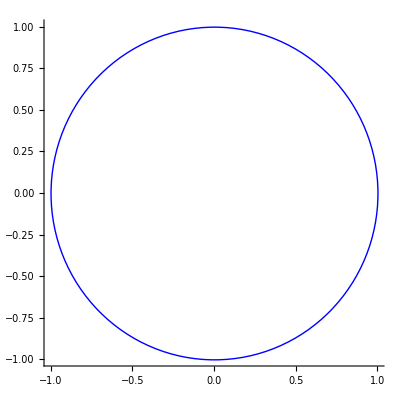

```mathematica
Show[
Graphics[
{Blue,Circle[{0,0}, 1]}
],
Axes->True, ImageSize->400
]
```

#### → 2) Tracer le vecteur unité sur l’axe des x (réels), et superposer

(optionnel : rajout de texte OverVector[e_1] à l’extrémité du vecteur, avec la fonction Text[])

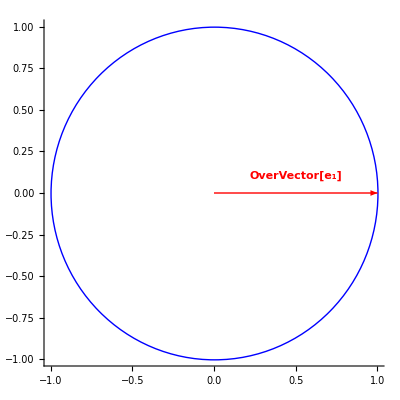

```mathematica
Show[Graphics[{
 Blue,Circle[{0,0}, 1],
Red,Thick,Arrow[{{0,0},{1,0}}],
Text[Style["OverVector[e_1]",Bold],{0.5,0.1}]
}],Axes->True, ImageSize->400]
```

#### → 3) Ajouter l’affichage du produit (Cos[θ] | -Sin[θ] Sin[θ] | Cos[θ]).(1 0) en bleu (prendre une rotation d’angle 60°)

(Flatten[] pourrait vous être utile ...)

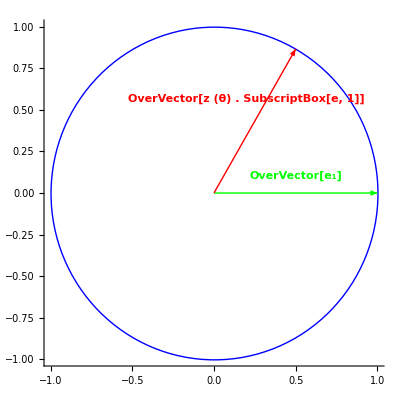

```mathematica
Show[Graphics[{
Blue,Circle[{0,0}, 1],
Green,Thick,Arrow[{{0,0},{1,0}}],
Text[Style["OverVector[e_1]",Bold],{0.5,0.1}],
Red,Thick,Arrow[{{0,0},Flatten[({{Cos[θ], -Sin[θ]}, {Sin[θ], Cos[θ]}}).({{1}, {0}})]}/.θ->π/3],
Text[Style["OverVector[z (θ) . SubscriptBox[e, 1]]",Bold],Flatten[({{Cos[θ], -Sin[θ]}, {Sin[θ], Cos[θ]}}).({{1}, {0}})]- 0.3/.θ->π/3]}],
Axes->True, ImageSize->400
]
```

#### → 4) En faire un Manipulate[], cadrer, jouer avec, et conclure.

```mathematica
Manipulate[
Show[
Graphics[
{Blue,Circle[{0,0}, 1],
Green,Thick,Arrow[{{0,0},{1,0}}],
Text[Style["OverVector[e_1]",Bold],{0.5,0.1}],
Red,Thick,Arrow[{{0,0},Flatten[({{Cos[θ], -Sin[θ]}, {Sin[θ], Cos[θ]}}).({{1}, {0}})]}],
Text[Style["OverVector[z (θ) . SubscriptBox[e, 1]]",Bold],Flatten[({{Cos[θ], -Sin[θ]}, {Sin[θ], Cos[θ]}}).({{1}, {0}})]-0.1]
}
],Axes->True,PlotRange->{{-1.2,1.2},{-1.2,1.2}},
AspectRatio->1,ImageSize->400
],
{{θ, π/3}, 0,2π}, SaveDefinitions->True
]
```

NB : On peut s’amuser à ouvrir la réglette sous le curseur, et à faire tourner automatiquement le vecteur bleu comme une pendule, et aussi jouer avec la stroboscopie...

Commentaires à faire :

## IV. Champ de Vecteurs

### B. VectorPlot de l’identité

#### → 1. Tracé brut du champ de vecteurs de l’identité

Tracer le champ de vecteurs (VectorPlot[]) de l’identité {x,y}, afficher-le entre -1 et 1 pour chaque dimension avec une taille ImageSize→150

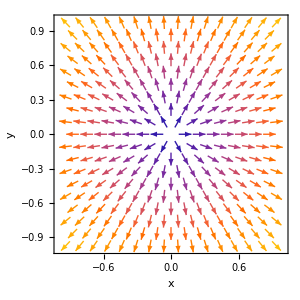

```mathematica
VectorPlot[
{x,y},{x,-1,1},{y,-1,1},
ImageSize->{300,300},FrameLabel->{x,y}
]
```

#### → 2. Tracé normalisé du champ de vecteurs de l’identité

Même tracé avec l’option VectorScale pour avoir de petites flèches de même longueur

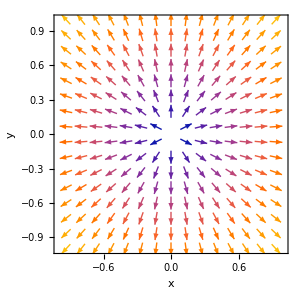

```mathematica
VectorPlot[
{x,y},{x,-1,1},{y,-1,1},
VectorScale->{Tiny,Automatic,None},
ImageSize->{300,300},FrameLabel->{x,y}
]
```

#### → 3. Idem + 1 ligne de flot

Même tracé avec l’option StreamPoints pour avoir de flot à partir du point {0.3,0.2}

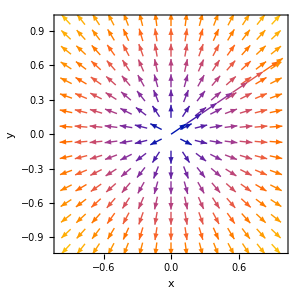

```mathematica
VectorPlot[
{x,y},{x,-1,1},{y,-1,1},
VectorScale->{Tiny,Automatic,None},
StreamPoints->{{{0.3,0.2}}},StreamStyle->{Red,Thick},
ImageSize->{300,300},FrameLabel->{x,y}
]
```

### → C. VectorPlot d’applications linéaires dans un Manipulate

#### → 1. VectorPlot d’une application linéaire simple dans un Manipulate

Dans le code ci-dessous, définir les coefficients a,b,c,et d à partir du tableau de matrices données ci dessous pour étudier le champ de vecteurs d’une application linéaire de votre choix :

Fonction |  Identité | Symétrie |  |  |  | 
 |  | Centrale | /X | /Y | /Y=X | Orthogonale/axe[θ]
Matrice | (λ | 0
0 | λ) | (-λ | 0
0 | -λ) | (λ | 0
0 | -λ) | (-λ | 0
0 | λ) | (0 | λ
λ | 0) | (λ Cos[θ] | λ Sin[θ]
λ Sin[θ] | -λ Cos[θ])
  |  |  |  |  |  | 
Fonction | Cisaillement[λ] | Rotation[θ] |  |  |  | Projection[θ]
Matrice | (1 | λ
0 | 1) | (λ Cos[θ] | -λ Sin[θ]
λ Sin[θ] | λ Cos[θ]) |  |  |  | (λ Cos[θ]^2 | λ Sin[θ]Cos[θ]
λ Sin[θ]Cos[θ] | λ Sin[θ]^2)

Le code utilise les 2 options de VectorPlot[], VectorScale et StreamPoints vues précédemment. 
Il comporte d’autres éléments de code intéressants : :
	l’objet original Locator pour déplacer interactivement un objet dans un graphique,
	des aspects d’affichage un peu techniques comme Control[], ou Style[], faciles à comprendre.

```mathematica
Manipulate[
(* I. -------Definitions et calcul des variables ----------------- *)
With[{a=λ Cos[θ],b=λ Sin[θ],c=λ Sin[θ],d=-λ Cos[θ]},
With[{mat=({{a, b}, {c, d}})},
(* II. -------Affichages ----------------------------------- *)
VectorPlot[
{a*x+b*y,c*x+d*y},{x,-1,1},{y,-1,1},
StreamPoints->{{p⟦1⟧,p⟦2⟧}},StreamStyle->{Red,Thick},VectorScale->{Tiny,Automatic,None},
ImageSize->{200,200},FrameLabel->{x,y}
]
]],
(* III. ------Contrôles des variables du Manipulate------------------ *)
Style["Matrice de Symétrie Orthogonale[λ, θ] :",Bold],
Control[{{λ,1,"λ"},-5,5,.01,Appearance->"Labeled"}],
Control[{{θ,0,"θ"},-π,π,.01,Appearance->"Labeled"}],
{{p,{.5,.5}},{-1,-1},{1,1},Locator}
]
```

#### → 2. Texte et VectorPlot dans deux colonnes adjacentes

Nous reprenons le code précédent en rajoutant au moyen de Eigensystem[] le calcul des valeurs propres, et des vecteurs propres de la matrice ainsi que de son déterminant au moyen de Det[].

Les changements de code servent principalement à présenter le texte et le VectorPlot dans deux colonnes au moyen :
	des fonctions Grid et Column d’organisation graphique en une colonne de texte et le graphique, et
	de la fonction TraditionalForm pour un bel affichage de texte.

```mathematica
Manipulate[
(* I. -------Definitions et calcul des variables ----------------- *)
With[{a=λ Cos[θ],b=λ Sin[θ],c=λ Sin[θ],d=-λ Cos[θ]},
With[{dvec=({{x'}, {y'}}),vec=({{x}, {y}}),mat=({{a, b}, {c, d}})},
With[(* Valeurs propres et vecteurs propres de la matrice *)
{esys=Eigensystem[mat],det=Det[mat] },
With[{
λ1=esys⟦1,1⟧,λ2=esys⟦1,2⟧,
vec1=({{esys⟦2,1⟧⟦1⟧}, {esys⟦2,1⟧⟦2⟧}}),vec2=({{esys⟦2,2⟧⟦1⟧}, {esys⟦2,2⟧⟦2⟧}})
},
(* II. -------Affichages --------------------------------- *)
Grid[{{
(* A. Texte de droite *)
Style[Text[Column[{
Text[TraditionalForm[Row[{"f : ℝ^2 ⟶ ℝ^2"}]]],
Text[TraditionalForm[Row[{"f :(x
y)↦(a | b
c | d)( x
 y)"}]]],
"",
Text[TraditionalForm[Row[{dvec , " = " , mat, vec}]]],
Text[TraditionalForm[Row[{" déterminant = ",det}]]],
"",
Text[TraditionalForm[Row[{"λ_1 = ",NumberForm[λ1,{5,2}]}]]],
Text[TraditionalForm[Row[{"λ_2 = ",NumberForm[λ2,{5,2}]}]]],
"",
Text[TraditionalForm[Row[{"ν_1 = ",NumberForm[vec1,{5,2}]}]]],
Text[TraditionalForm[Row[{"ν_2 = ",NumberForm[vec2,{5,2}]}]]],
"                                                      "
}]],12],
(* B. Figure de gauche *)
VectorPlot[
{a*x+b*y,c*x+d*y},{x,-1,1},{y,-1,1},
StreamPoints->{{p⟦1⟧,p⟦2⟧}},StreamStyle->{Red,Thick},VectorScale->{Tiny,Automatic,None},
ImageSize->{250,250},FrameLabel->{x,y}
]
}}]
]]]],
(* III. ------Contrôles des variables du Manipulate---------------- *)
Style["Paramètres de la matrice de Symétrie Orthogonale :",Bold],
Control[{{λ,1,"λ"},-5,5,.01,Appearance->"Labeled"}],
Control[{{θ,0,"θ"},-π,π,.01,Appearance->"Labeled"}],
{{p,{.5,.5}},{-1,-1},{1,1},Locator}
]
```

Jouer avec les curseurs et le locateur dans tout l’espace....

## → V. Expressions des Solutions d’EDO avec Mathematica

### → A. Résolution Formelle

#### → 1. Résolution formelle d'EDO non linéaires

a./ Résoudre l’équation différentielle suivante :
	(ⅆ x)/(ⅆ t)=x (a-b x)-c	où a, b, c sont positives ou nulles

```mathematica
solFormelle[a_,b_,c_,d_,t_]=Simplify[
x[t]/.DSolve[{
x'[t]==x[t](a-b x[t])-c,
x[0]==d
},x[t],t
]]⟦1⟧
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

(a-√(-a^2+4 b c) Tan[1/2 √(-a^2+4 b c) t-ArcTan[(-a+2 b d)/(√(-a^2+4 b c))]])/(2 b)

b./ Définir une fonction de  a, b, c, d, et t qui mémorise l’expression de la solution :

```mathematica
solFormelle[a,b,c,d,tt]/.{a->1,b->0.02,c->0,d->0.01}//Chop
```

25. (1-1. Tanh[4.2585-0.5 tt])

c./ Tracer la solution pour a=1, b=0.02, c=0, d=0.01, t=20

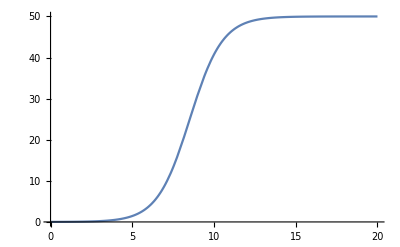

```mathematica
Plot[
solFormelle[a,b,c,d,t]/.{a->1,b->0.02,c->0,d->0.01},
{t,0,20},
PlotRange->{{0,20},All}
]
```

d./ Tracer la solution générale avec un Manipulate[] pour des valeurs raisonnables de  a, b, c, d et t :

```mathematica
Manipulate[
Plot[
solFormelle[a,b,c,d,t],
{t,0,tTot},
PlotRange->{{0,tTot},All}
],
{{a,1},0,10},
{{b,0.02},0,1},
{{c,0},0,2},
{{d,0.01},0,2},
{{tTot,20},0.001,100}
]
```

#### → 2. Résolution formelle d'EDO linéaires

a./ Soit : A=(a | b
c | d), X=(x(t)
y(t))  et B=(b1
b2), résoudre le problème de Cauchy suivant :
	(ⅆ X)/(ⅆ t)=A X+B	∀t∈ℝ 
	X0=(x0
y0)  à t=0

```mathematica
res=DSolve[{
x'[t]==a*x[t]+b*y[t],
y'[t]==c*x[t]+d*y[t],
x[0]==x0, y[0]==y0
},{x[t], y[t]},t
]//Simplify
```

{{x[t]→1/(2 √(a^2+4 b c-2 a d+d^2))ⅇ^(1/2 (a+d-√(a^2+4 b c-2 a d+d^2)) t) (√(a^2+4 b c-2 a d+d^2) x0+√(a^2+4 b c-2 a d+d^2) ⅇ^(√(a^2+4 b c-2 a d+d^2) t) x0+a (-1+ⅇ^(√(a^2+4 b c-2 a d+d^2) t)) x0-d (-1+ⅇ^(√(a^2+4 b c-2 a d+d^2) t)) x0-2 b y0+2 b ⅇ^(√(a^2+4 b c-2 a d+d^2) t) y0),y[t]→1/(2 √(a^2+4 b c-2 a d+d^2))ⅇ^(1/2 (a+d-√(a^2+4 b c-2 a d+d^2)) t) (2 c (-1+ⅇ^(√(a^2+4 b c-2 a d+d^2) t)) x0+(a-a ⅇ^(√(a^2+4 b c-2 a d+d^2) t)+d (-1+ⅇ^(√(a^2+4 b c-2 a d+d^2) t))+√(a^2+4 b c-2 a d+d^2) (1+ⅇ^(√(a^2+4 b c-2 a d+d^2) t))) y0)}}

b./ Tracer la solution pour a=-1, b=2, c=3, d=-4, x0=1, y0=0, t alllant de 0 à 2.

{{(ⅇ^(1/2 (5-√33) t) (-1+√33+ⅇ^(√33 t)+√33 ⅇ^(√33 t)-4 (-1+ⅇ^(√33 t))))/(2 √33),√(3/11) ⅇ^(1/2 (5-√33) t) (-1+ⅇ^(√33 t))}}

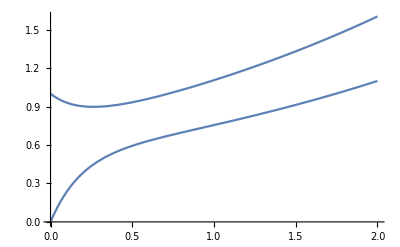

```mathematica
{x[t], y[t]}/.res/.{a->1,b->2,c->3,d->4,x0->1,y0->0}
Plot[
{x[t], y[t]}/.res/.{a->-1,b->2,c->3,d->-4,x0->1,y0->0},{t,0,2}
]
```

## → VI. Résolution pratique d’EDO numériques

### A. Résolution du système d'EDO pour e_0/(K_m+s_0)<<1

a./ Résoudre le système d’équations différentielles suivant :
	(ⅆ s)/(ⅆ t)(t)=-k1 e0 s(t)+(k1 s(t)+kr1) c(t)		∀t∈ℝ
	(ⅆ c)/(ⅆ t)(t)=k1 e0 s(t)-(k1 s(t)+kr1+k2) c(t)	
avec 	k1=10^4  en mM^-1 s^-1; k2=10^3 s^-1,kr1=10^3 s^-1
et les concentrations initiales :	e0=10^-3 mM, s0=1 mM (excès de substrat).

```mathematica
solutionF[k1_:10^4,k2_:10^3,kr1_:10^3,e0_:10^-3,s0_:1,tTot_:10^-3]:=NDSolve[
{
s'[t]==-(k1*e0)*s[t]+(k1*s[t]+kr1)*c[t],
c'[t]==(k1*e0)*s[t]-(k1*s[t]+kr1+k2)*c[t],
p'[t]==k2*c[t],
s[0]==s0, c[0]==0,  p[0]==0
},
{s[t], c[t],p[t]},
{t,0,tTot}
]
solutionF[]==solutionF[(*k1*)10^4,(*k2*)10^3,(*kr1*)10^3,(*e0*)10^-3,(*s0*)1,(*tTot*)10^-3];
```

b./ Tracer les solutions :

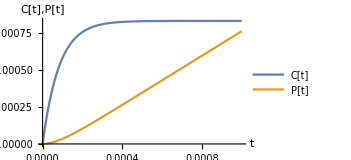

```mathematica
Plot[
Evaluate[{c[t],p[t]}/.solutionF[]],{t,0,1/10^3},
AxesLabel->{"t","C[t],P[t]"},PlotRange->All,
PlotLegends->{"C[t]","P[t]"},ImageSize->260
]
```

## Exercices EDO

## → I. Elaboration d’un Manipulate pour EDO

### → A. VectorPlot de 9 applications linéaires fonctions de λ et/ou θ

Champ de vecteurs 9 applications linéaires fondamentales d’angle θ, et/ou d’homothétie H[λ] de rapport λ

#### → 1. Manipulate pour afficher une matrice parmi 9

En utilisant les définitions de matrices ci-dessous, écrire un Manipulate pour afficher l’une de ces matrices au choix ainsi que le premier coefficient de la matrice :

```mathematica
(* -------Liste de choix de 9 matrices 2D pour Manipulate --------- *)
(* Identite H[λ] *)matIdλ[λ_,θ_]:=({{λ, 0}, {0, λ}})
(* SymetrieCentrale H[λ]*) matSymCentλ[λ_,θ_]:=({{-λ, 0}, {0, -λ}})
(* Symetrie/X H[λ] *) matSymXλ[λ_,θ_]:=({{λ, 0}, {0, -λ}})
(* Symetrie/Y H[λ] *) matSymYλ[λ_,θ_]:=({{-λ, 0}, {0, λ}})
(* Symetrie/Y=X H[λ] *) matSymYeqXλ[λ_,θ_]:=({{0, λ}, {λ, 0}})
(* SymetrieOrthogonale/axe[θ] H[λ] *) matSymλθ[λ_,θ_]:=({{λ Cos[θ], λ Sin[θ]}, {λ Sin[θ], -λ Cos[θ]}})
(* Rotation[θ] H[λ] *) matRotλθ[λ_,θ_]:=({{λ Cos[θ], -λ Sin[θ]}, {λ Sin[θ], λ Cos[θ]}})
(* Projection[θ] H[λ] *) matProjλθ[λ_,θ_]:=({{λ Cos[θ]^2, λ Sin[θ]Cos[θ]}, {λ Sin[θ]Cos[θ], λ Sin[θ]^2}})
(* Cisaillement[λ] *) matCisλ[λ_,θ_]:=({{1, λ}, {0, 1}}) 
(* ---------------------------------------------------------------- *)
```

```mathematica
Manipulate[

]
```

#### → 2. Manipulate pour tracer le champ de vecteurs d’une matrice parmi 9

En reprenant le code ci-dessus, compléter ce Manipulate pour tracer le champ de vecteurs d’une matrice parmi 9 :

```mathematica
Manipulate[
VectorPlot[


],
Style["Choix de Matrices particulières ",Bold],
{{mat,matIdλ},{matIdλ,matSymCentλ,matSymXλ,matSymYλ,matSymYeqXλ,matSymλθ,matRotλθ,matProjλθ,matCisλ}},
Control[{{λ,1,"λ"},-5,5,.01,Appearance->"Labeled"}],
Control[{{θ,0,"θ"},-π,π,.01,Appearance->"Labeled"}],
(* Point P des Initialisations de la ligne du champ de vecteurs *)
{{p,{.5,.5}},{-1,-1},{1,1},Locator}
]
```

#### → 3. Texte et VectorPlot dans deux colonnes adjacentes dans un Manipulate de 9 matrices possibles

Avec le code vu en préambule, on obtient le Manipulate plus complet dont vous étudierez le code et les effets.

```mathematica
Manipulate[
(* I. -------Definitions et calcul des variables ------------------- *)
With[{dvec=({{x'}, {y'}}),vec=({{x}, {y}})},
With[(* Calcul des valeurs propres et des vecteurs propres de la matrice *)
{esys=Eigensystem[mat[λ,θ]],det=Det[mat[λ,θ]] },
With[{λ1=esys⟦1,1⟧,λ2=esys⟦1,2⟧,
vec1=({{esys⟦2,1⟧⟦1⟧}, {esys⟦2,1⟧⟦2⟧}}),vec2=({{esys⟦2,2⟧⟦1⟧}, {esys⟦2,2⟧⟦2⟧}})
},
(* II. -------Affichages ---------------------------------------- *)
Grid[{{
(* A. Texte de droite *)
Style[Text[Column[{
Text[TraditionalForm[Row[{"f : ℝ^2 ⟶ ℝ^2"}]]],
Text[TraditionalForm[Row[{"f :(x
y)↦(a | b
c | d)( x
 y)"}]]],
"",
Text[TraditionalForm[Row[{dvec , " = " ,  mat[λ,θ], vec}]]],
Text[TraditionalForm[Row[{" déterminant = ",det}]]],
"",
Text[TraditionalForm[Row[{"λ_1 = ",NumberForm[λ1,{5,2}]}]]],
Text[TraditionalForm[Row[{"λ_2 = ",NumberForm[λ2,{5,2}]}]]],
"",
Text[TraditionalForm[Row[{"ν_1 = ",NumberForm[vec1,{5,2}]}]]],
Text[TraditionalForm[Row[{"ν_2 = ",NumberForm[vec2,{5,2}]}]]],
"                                                      "
}]],12],
(* B. Figure de gauche *)
VectorPlot[
{mat[λ,θ]⟦1,1⟧ x+ mat[λ,θ]⟦1,2⟧ y, mat[λ,θ]⟦2,1⟧ x+mat[λ,θ]⟦2,2⟧ y},{x,-1,1},{y,-1,1},
StreamPoints->{{p⟦1⟧,p⟦2⟧}},StreamStyle->{Red,Thick},VectorScale->{Tiny,Automatic,None},
ImageSize->{300,300},FrameLabel->{x,y}
]
}}]
]]],
(* III. ------Contrôles des variables du Manipulate---------------- *)
Style["Choix de Matrices particulières fonction de λ et θ ",Bold],
{{mat,matSymλθ},{matIdλ,matSymCentλ,matSymXλ,matSymYλ,matSymYeqXλ,matSymλθ,matRotλθ,matProjλθ,matCisλ}},
Control[{{λ,1,"λ"},-5,5,.01,Appearance->"Labeled"}],
Control[{{θ,π/3,"θ"},-π,π,.01,Appearance->"Labeled"}],
(* Point P des Initialisations de la ligne du champ de vecteurs *)
{{p,{.5,.5}},{-1,-1},{1,1},Locator}
]
```

Part::partw: Part 2 of Eigensystem[matSymλθ[1,π/3]] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partd: Part specification matSymλθ[1,π/3]⟦1,1⟧ is longer than depth of object.

Part::partd: Part specification matSymλθ[1,π/3]⟦1,2⟧ is longer than depth of object.

Part::partd: Part specification matSymλθ[1,π/3]⟦1,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

a./ Pour les matrices : Identité H[λ], les symétries H[λ], en quoi change le champ de vecteurs en fonction de λ ?

b./ Avec une matrice de rotation, pour quelles valeurs d’angle θ, obtient-on :
	un flot circulaire ? 
	
	en colimaçon allant vers {0,0}, 
	
	allant vers l’infini ?

c./ Y-a-t-il des axes de symétrie dans le cas des 
	symétries ?
	
	rotations ?
	
	projections ?
	
	des cisaillements ?
	
Expliquez votre réponse à partir de :
	l’observation du champ de vecteurs
	
	et de tout autre élément

#### → 4. Idem + matrice générale + Axes de symétrie et vecteurs propres

On rajoute la possibilité de traiter une matrice réelle générale en activant le “generalFlag”, et en contrôlant les valeurs des coefficients a, b, c, d de cette matrice.

Reprendre la question précédente c./ avec le Manipulate ci-dessous

c./ Y-a-t-il des axes de symétrie dans le cas des 
	symétries ?
	
	rotations ?
	
	projections ?
	
	des cisaillements ?
	
	des matrices générales ?
	
Expliquez votre réponse à partir de :
	l’observation du champ de vecteurs
	
	et de tout autre élément

```mathematica
Manipulate[
(* I. -------Definitions et calcul des variables ------------------- *)
With[{dvec=({{x'}, {y'}}),vec=({{x}, {y}}), matCalc=If[generalFlag,({{a, b}, {c, d}}),mat[λ,θ]]},
With[(* Valeurs propres et vecteurs propres de la matrice *)
{esys=Eigensystem[matCalc],det=Det[matCalc] },
With[{λ1=esys⟦1,1⟧,λ2=esys⟦1,2⟧,
vec1=({{esys⟦2,1⟧⟦1⟧}, {esys⟦2,1⟧⟦2⟧}}),vec2=({{esys⟦2,2⟧⟦1⟧}, {esys⟦2,2⟧⟦2⟧}})
},
(* II. -------Affichages --------------------------------------- *)
Grid[{{
(* A. Texte de droite *)
Style[Text[Column[{
Text[TraditionalForm[Row[{"f : ℝ^2 ⟶ ℝ^2"}]]],
Text[TraditionalForm[Row[{"f :(x
y)↦(a | b
c | d)( x
 y)"}]]],
"",
Text[TraditionalForm[Row[{dvec , " = " ,  matCalc, vec}]]],
Text[TraditionalForm[Row[{" déterminant = ",det}]]],
"",
Text[TraditionalForm[Row[{"λ_1 = ",NumberForm[λ1,{5,2}]}]]],
Text[TraditionalForm[Row[{"λ_2 = ",NumberForm[λ2,{5,2}]}]]],
"",
Text[TraditionalForm[Row[{"ν_1 = ",NumberForm[vec1,{5,2}]}]]],
Text[TraditionalForm[Row[{"ν_2 = ",NumberForm[vec2,{5,2}]}]]],
"                                                      "
}]],12],
(* B. Figure de gauche *)
Show[
(* Champ de vecteurs *)
VectorPlot[
{matCalc⟦1,1⟧ x+ matCalc⟦1,2⟧ y, matCalc⟦2,1⟧ x+matCalc⟦2,2⟧ y},
{x,-1,1},{y,-1,1},
StreamPoints->{{p⟦1⟧,p⟦2⟧}},StreamStyle->{Red,Thick},VectorScale->{Tiny,Automatic,None},
ImageSize->{300,300},FrameLabel->{x,y}
],
(* Axes des vecteurs propres réels *)
Graphics[{
Thick,Orange,
Map[
Line[{-100#,100#}]&,
Select[Eigenvectors[matCalc],(Im[#⟦1⟧]==0&&Im[#⟦2⟧]==0)&]
]
}]
](* Fin de Show *)
}}](* Fin de Grid *)
]]](* Fin des With *),
(* III. ------Contrôles des variables du Manipulate---------------- *)
(* A. Liste des choix de matrices *)
Style["Choix de Matrices particulières fonction de λ et θ ",Bold],
{{mat,matSymλθ},{matIdλ,matSymCentλ,matSymXλ,matSymYλ,matSymYeqXλ,matSymλθ,matRotλθ,matProjλθ,matCisλ}},
(* B. Contrôles des paramètres numériques *)
(* Matrices particulières fonction de λ ou θ *)
Row[{
Control[{{λ,1,"λ"},-5,5,.01,Appearance->"Labeled"}],
Control[{{θ,π/3,"θ"},-π,π,.01,Appearance->"Labeled"}]
}],
(* Point P des Initialisations de la ligne du champ de vecteurs *)
{{p,{.5,.5}},{-1,-1},{1,1},Locator},
(* Matrices "General[a,b,c,d]" avec initialisation Romeo et Juliette *)
{{generalFlag,False},{True,False}},
Style["Matrices générales fonction de a, b, c, d ",Bold],
Row[{
Control[{{a,.5,"a"},-1,1,.01,Appearance->"Labeled"}],
Control[{{b,-.75,"b"},-1,1,.01,Appearance->"Labeled"}]
}],
Row[{
Control[{{c,.1,"c"},-1,1,.01,Appearance->"Labeled"}],
Control[{{d,.5,"d"},-1,1,.01,Appearance->"Labeled"}]
}]
]
```

Part::partw: Part 2 of Eigensystem[matSymλθ[1,π/3]] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partd: Part specification matSymλθ[1.,1.0472]⟦1,1⟧ is longer than depth of object.

Part::partd: Part specification matSymλθ[1.,1.0472]⟦1,2⟧ is longer than depth of object.

Part::partd: Part specification matSymλθ[1.,1.0472]⟦1,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

### → B. VectorPlot de 10 applications linéaires + solutions EDO

#### → 1. Idem + calcul et affichage des solutions EDO

On rajoute :
	la partie calcul des EDO à la fin de I. Définitions et calcul des variables, et 
	le tracé des solutions à la fin de II. Affichage,
	le contrôle du temps total de calcul de l’EDO à la fin du III. Contrôles des variables du Manipulate.

La solution de l’EDO est tracée en pointillés noirs à partir du point P donné par le “Locator”.

```mathematica
Manipulate[
(* I. -------Definitions et calcul des variables ------------------- *)
With[{dvec=({{x'}, {y'}}),vec=({{x}, {y}}), matCalc=If[generalFlag,({{a, b}, {c, d}}),mat[λ,θ]]},
With[(* Valeurs propres et vecteurs propres de la matrice *)
{esys=Eigensystem[matCalc],det=Det[matCalc] },
With[{λ1=esys⟦1,1⟧,λ2=esys⟦1,2⟧,
vec1=({{esys⟦2,1⟧⟦1⟧}, {esys⟦2,1⟧⟦2⟧}}),vec2=({{esys⟦2,2⟧⟦1⟧}, {esys⟦2,2⟧⟦2⟧}})
},
With[(* Solution EDO de R[t] et J[t] initialisées avec P Locator *)
{solu = NDSolve[{
R'[t] == matCalc⟦1,1⟧ R[t]+ matCalc⟦1,2⟧  J[t],
J'[t] == matCalc⟦2,1⟧  R[t]+ matCalc⟦2,2⟧  J[t],
R[0]==p⟦1⟧, J[0]==p⟦2⟧}, {R[t], J[t]}, {t, 0, T},
 PrecisionGoal -> 3
] },
(* II. -------Affichages --------------------------------------- *)
Grid[{{
(* A. Texte de droite *)
Style[Text[Column[{
Text[TraditionalForm[Row[{"f : ℝ^2 ⟶ ℝ^2"}]]],
Text[TraditionalForm[Row[{"f :(x
y)↦(a | b
c | d)( x
 y)"}]]],
"",
Text[TraditionalForm[Row[{dvec , " = " ,  matCalc, vec}]]],
Text[TraditionalForm[Row[{" déterminant = ",det}]]],
"",
Text[TraditionalForm[Row[{"λ_1 = ",NumberForm[λ1,{5,2}]}]]],
Text[TraditionalForm[Row[{"λ_2 = ",NumberForm[λ2,{5,2}]}]]],
"",
Text[TraditionalForm[Row[{"ν_1 = ",NumberForm[vec1,{5,2}]}]]],
Text[TraditionalForm[Row[{"ν_2 = ",NumberForm[vec2,{5,2}]}]]],
"                                                      "
}]],12],
(* B. Figure de gauche *)
Show[
(* Champ de vecteurs *)
VectorPlot[
{matCalc⟦1,1⟧ x+ matCalc⟦1,2⟧ y, matCalc⟦2,1⟧ x+matCalc⟦2,2⟧ y},
{x,-1,1},{y,-1,1},
StreamPoints->{{p⟦1⟧,p⟦2⟧}},StreamStyle->{Red,Thick},VectorScale->{Tiny,Automatic,None},
ImageSize->{300,300},FrameLabel->{x,y}
],
(* Axes des vecteurs propres réels *)
Graphics[{
Thick,Orange,
Map[
Line[{-100#,100#}]&,
Select[Eigenvectors[matCalc],(Im[#⟦1⟧]==0&&Im[#⟦2⟧]==0)&]
]
}],
(* Tracé de la solution de l'équation différentielle *)
ParametricPlot[
Evaluate[{R[t],J[t]}/.solu⟦1⟧ ], {t, 0, T},
PlotRange -> All,PlotStyle -> {Black, Dashed},
AspectRatio -> 1,
MaxRecursion -> ControlActive[Automatic, 8]
]
](* Fin de Show *)
}}](* Fin de Grid *)
]]]](* Fin des With *),
(* III. ------Contrôles des variables du Manipulate---------------- *)
(* A. Liste des choix de matrices *)
Style["Choix de Matrices particulières fonction de λ et θ ",Bold],
{{mat,matIdλ},{matIdλ,matSymCentλ,matSymXλ,matSymYλ,matSymYeqXλ,matSymλθ,matRotλθ,matProjλθ,matCisλ}},
(* B. Contrôles des paramètres numériques *)
(* Matrices particulières fonction de λ ou θ *)
Row[{
Control[{{λ,1,"λ"},-5,5,.01,Appearance->"Labeled"}],
Control[{{θ,0,"θ"},-π,π,.01,Appearance->"Labeled"}]
}],
(* Point P des Initialisations de la ligne du champ de vecteurs *)
{{p,{.5,.5}},{-1,-1},{1,1},Locator},
(* Matrice generale[a,b,c,d]" avec initialisation Romeo et Juliette *)
{{generalFlag,False},{True,False}},
Style["Matrices générales fonction de a, b, c, d ",Bold],
Row[{
Control[{{a,.5,"a"},-1,1,.01,Appearance->"Labeled"}],
Control[{{b,-.75,"b"},-1,1,.01,Appearance->"Labeled"}]
}],
Row[{
Control[{{c,.1,"c"},-1,1,.01,Appearance->"Labeled"}],
Control[{{d,.5,"d"},-1,1,.01,Appearance->"Labeled"}]
}],
(* Equations différentielles *)
Control[{{T,10.0,"temps d'intégration"},0.1,20.0,.1,Appearance->"Labeled"}]
]
```

Part::partw: Part 2 of Eigensystem[matIdλ[1,0]] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partd: Part specification matIdλ[1,0]⟦1,1⟧ is longer than depth of object.

Part::partd: Part specification matIdλ[1,0]⟦1,2⟧ is longer than depth of object.

Part::partd: Part specification matIdλ[1,0]⟦2,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

ReplaceAll::reps: {R'[t]==J[t] matIdλ[1,0]⟦1,2⟧+matIdλ[1,0]⟦1,1⟧ R[t],J'[t]==J[t] matIdλ[1,0]⟦2,2⟧+matIdλ[1,0]⟦2,1⟧ R[t],R[0]==0.5,J[0]==0.5} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {R'[0.000204082]==J[0.000204082] matIdλ[1,0]⟦1,2⟧+matIdλ[1,0]⟦1,1⟧ R[0.000204082],J'[0.000204082]==J[0.000204082] matIdλ[1,0]⟦2,2⟧+matIdλ[1,0]⟦2,1⟧ R[0.000204082],R[0]==0.5,J[0]==0.5} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {R'[0.000204082]==J[0.000204082] matIdλ[1.,0.]⟦1,2⟧+matIdλ[1.,0.]⟦1,1⟧ R[0.000204082],J'[0.000204082]==J[0.000204082] matIdλ[1.,0.]⟦2,2⟧+matIdλ[1.,0.]⟦2,1⟧ R[0.000204082],R[0.]==0.5,J[0.]==0.5} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

→ a./ Quel est l’élément nouveau ?

→ b./ Qu’observez-vous ?

### → C. VectorPlot de 10 (applications + EDO) linéaires + cas non linéaire

#### 1. Redéfinition des matrices sans homothétie (À VALIDER)

L’homothétie de rapport λ complique beaucoup les calculs, alors qu’elle n’a pas d’effet dans VectorPlot qui remet à l’échelle. On introduit donc d’abord la simplification des matrices ci-dessous.
Dans le code du Manipulate, il suffit de changer une fois mat[λ,θ] en mat[θ] dans le code ci-dessous, et de modifier le contrôle des matrices avec les noms sans λ, mais avec seulement θ.

```mathematica
(* -------Liste de choix de 9 matrices 2D pour Manipulate --------- *)
(* Simplification en supprimant H[λ] l'homothétie de rapport λ *)
(* Identite *)                                         matId[ϕ_]:=({{1, 0}, {0, 1}})
(* SymetrieCentrale *)                       matSymCent[ϕ_]:=({{-1, 0}, {0, -1}})
(* Symetrie/X *)                                     matSymX[ϕ_]:=({{1, 0}, {0, -1}})
(* Symetrie/Y *)                                     matSymY[ϕ_]:=({{-1, 0}, {0, 1}})
(* Symetrie/Y=X *)                                 matSymYeqX[θ_]:=({{0, 1}, {1, 0}})
(* SymetrieOrthogonale/axe[θ] *) matSymθ[θ_]:=({{Cos[θ], Sin[θ]}, {Sin[θ], -Cos[θ]}})
(* Rotation[ϕ] *)                                   matRotθ[θ_]:=({{Cos[θ], -Sin[θ]}, {Sin[θ], Cos[θ]}})
(* Projection[ϕ] *)  matProjθ[θ_]:=({{Cos[θ]^2, Sin[θ]Cos[θ]}, {Sin[θ]Cos[θ], Sin[θ]^2}})
(* Cisaillement[ϕ] *)                          matCisθ[θ_]:=({{1, θ}, {0, 1}}) 
(* ---------------------------------------------------------------- *)
```

#### → 2. Ajout d’un cas EDO non linéaire (Roméo et Juliette)

Puis on introduit la la possibilité de termes non linéaires dans la matrice, et dans l’EDO. Pour cela, il faut procéder aux modifications suivantes.

Dans  I. Définitions et calcul des variables, il faut :
	* remplacer la matrice(a | b 
c  | d) par
	 (a | b If[includeNonlinearTerms,JM-Abs[y] , 1]
c If[includeNonlinearTerms,RM-Abs[x] , 1]  | d)
	** remplacer mat[λ,θ] par mat[θ]
	*** faire les substitutions /.{Abs[y]→ Abs[J[t]] et /.{Abs[x]→ Abs[R[t]] dans les EDO.

À la fin du III. Contrôles des variables du Manipulate, il suffit de :
	supprimer le contrôle de λ, et
	d’ajouter le contrôle des coefficients non linéaires portant sur JM et RM de l’EDO .

```mathematica
Manipulate[
(* I. -------Definitions et calcul des variables ------------------- *)
With[{dvec=({{x'}, {y'}}),vec=({{x}, {y}}), 
(* On rajoute éventuellement les termes non linéaires de l'EDO de Roméo et Juliette *)
matCalc=If[generalFlag,
({{a, b If[includeNonlinearTerms,JM-Abs[y] , 1]}, {c If[includeNonlinearTerms,RM-Abs[x] , 1], d}}),
mat[θ]]
},
With[(* Valeurs propres et vecteurs propres de la matrice *)
{esys=Eigensystem[matCalc],det=Det[matCalc] },
With[{λ1=esys⟦1,1⟧,λ2=esys⟦1,2⟧,
vec1=({{esys⟦2,1⟧⟦1⟧}, {esys⟦2,1⟧⟦2⟧}}),vec2=({{esys⟦2,2⟧⟦1⟧}, {esys⟦2,2⟧⟦2⟧}})
},
With[(* Solution EDO de R[t] et J[t] initialisées avec P Locator *)
{solu = NDSolve[{
R'[t] ==  matCalc⟦1,1⟧ R[t]+( matCalc⟦1,2⟧ J[t]/.{Abs[y]-> Abs[J[t]]}),
J'[t] == (matCalc⟦2,1⟧ R[t]/.{Abs[x]-> Abs[R[t]]})+  matCalc⟦2,2⟧ J[t],
R[0]==p⟦1⟧, J[0]==p⟦2⟧}, {R[t], J[t]}, {t, 0, T},
 PrecisionGoal -> 3
]//Quiet(* Supprime messages : NDSolve : equations stiff *)
},
(* II. -------Affichages --------------------------------------- *)
Grid[{{
(* A. Texte de droite *)
Style[Text[Column[{
Text[TraditionalForm[Row[{"f : ℝ^2 ⟶ ℝ^2"}]]],
Text[TraditionalForm[Row[{"f :(x
y)↦(a | b
c | d)( x
 y)"}]]],
"",
Text[TraditionalForm[Row[{dvec , " = " ,  matCalc, vec}]]],
Text[TraditionalForm[Row[{" déterminant = ",det}]]],
"",
Text[TraditionalForm[Row[{"λ_1 = ",NumberForm[λ1,{5,2}]}]]],
Text[TraditionalForm[Row[{"λ_2 = ",NumberForm[λ2,{5,2}]}]]],
"",
Text[TraditionalForm[Row[{"ν_1 = ",NumberForm[vec1,{5,2}]}]]],
Text[TraditionalForm[Row[{"ν_2 = ",NumberForm[vec2,{5,2}]}]]],
"                                                      "
}]],12],
(* B. Figure de gauche *)
Show[
(* Champ de vecteurs *)
VectorPlot[
{matCalc⟦1,1⟧ x+ matCalc⟦1,2⟧ y, matCalc⟦2,1⟧ x+matCalc⟦2,2⟧ y},
{x,-1,1},{y,-1,1},
StreamPoints->{{p⟦1⟧,p⟦2⟧}},StreamStyle->{Red,Thick},VectorScale->{Tiny,Automatic,None},
ImageSize->{300,300},FrameLabel->{x,y}
],
(* Axes des vecteurs propres réels *)
Graphics[{
Thick,Orange,
Map[
Line[{-100#,100#}]&,
Select[Eigenvectors[matCalc],(Im[#⟦1⟧]==0&&Im[#⟦2⟧]==0)&]
]
}],
(* Tracé de la solution de l'équation différentielle *)
ParametricPlot[
Evaluate[{R[t],J[t]}/.solu⟦1⟧ ], {t, 0, T},
PlotRange -> All,PlotStyle -> {Black, Dashed},
AspectRatio -> 1,
MaxRecursion -> ControlActive[Automatic, 8]
]
](* Fin de Show *)
}}](* Fin de Grid *)
]]]](* Fin des With *),
(* III. ------Contrôles des variables du Manipulate---------------- *)
(* A. Liste des choix de matrices *)
Style["Choix de Matrices particulières fonction de λ et θ ",Bold],
{{mat,matId},{matId,matSymCent,matSymX,matSymY,matSymYeqX,matSymθ,matRotθ,matProjθ,matCisθ}},
(* B. Contrôles des paramètres numériques *)
(* Matrices particulières fonction de λ ou θ *)
Control[{{θ,0,"θ"},-π,π,.01,Appearance->"Labeled"}],
(* Point P des Initialisations de la ligne du champ de vecteurs *)
{{p,{.5,.5}},{-1,-1},{1,1},Locator},
(* Matrice generale[a,b,c,d]" avec initialisation Romeo et Juliette *)
{{generalFlag,False},{True,False}},
Style["Matrices générales fonction de a, b, c, d ",Bold],
Row[{
Control[{{a,.5,"a"},-1,1,.01,Appearance->"Labeled"}],
Control[{{b,-.75,"b"},-1,1,.01,Appearance->"Labeled"}]
}],
Row[{
Control[{{c,.1,"c"},-1,1,.01,Appearance->"Labeled"}],
Control[{{d,.5,"d"},-1,1,.01,Appearance->"Labeled"}]
}],
(* Equations différentielles *)
Control[{{T,10.0,"temps d'intégration"},0.1,20.0,.1,Appearance->"Labeled"}],
Delimiter,
"include negative effect of too much love (non linéarité) :  ",{{includeNonlinearTerms, False, ""}, {True, False}},
Row[{
Dynamic[Style[ "Juliet's love for Romeo\nbecomes counterproductive.", If[includeNonlinearTerms, Blue, Lighter[Gray]]]],
Control[{{JM, 0.3,""}, 0, 5, ImageSize -> Small,Appearance->"Labeled"}],
Dynamic[Style["Romeo's love for Juliet\nbecomes counterproductive.", If[includeNonlinearTerms, Blue, Lighter[Gray]]]],
Control[{{RM, 0.6, ""}, 0, 5, ImageSize -> Small,Appearance->"Labeled"}]
}],SaveDefinitions->True
]
```

→ a./ Qu’observez-vous ?